## Circuit 1: Serial LRC Circuit

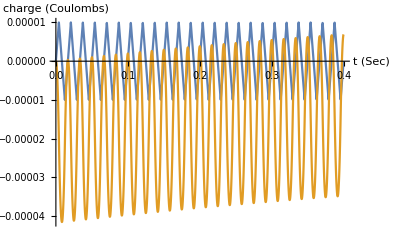

```mathematica
Clear[V,t]
TMax=0.4;
{R1,C2,L3}={100.,0.01,0.01};
V[t_]:=TriangleWave[60 t]
qSol=NDSolveValue[{
V[t]+ R1 q'[t]+ q[t]/C2 + L3 q''[t]==0,
q[0]==0,q'[0]==0},
q,{t, 0, TMax}];
Plot[{0.00001 V[t],qSol[t]}, {t, 0, TMax},
AxesLabel->{"t (Sec)","charge (Coulombs)"}]
```

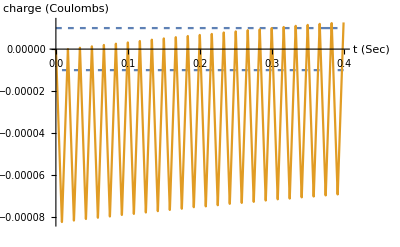

```mathematica
Clear[V,t]
TMax=0.4;
{R1,C2,L3}={100.,0.01,0.01};
V[t_]:=SquareWave[60 t]
qSol=NDSolveValue[{
V[t]+ R1 q'[t]+ q[t]/C2 + L3 q''[t]==0,
q[0]==0,q'[0]==0},
q,{t, 0, TMax}];
Plot[{0.00001 V[t],qSol[t]}, {t, 0, TMax},
AxesLabel->{"t (Sec)","charge (Coulombs)"}]
```